```mathematica
Clear[datdensity,colorfunc,rng,P1]
```

```mathematica
datdensity=Import["saved_plots/NHChern/all_states_other_than_two_topological/m_in_paper-1/hx0hy0hz0/OBC_statesLx_28Ly_28biorthogonal.dat"];
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]];*)
```

```mathematica
(*colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];*)
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,0.8]];
```

```mathematica
rngOld={0,Max[#]}&@datdensity[[All,3]]
```

{0,0.00255428}

```mathematica
rng={0,0.0026}
```

{0,0.0026}

```mathematica
Dimensions[datdensity]
```

{784,3}

```mathematica
FilteredData=Select[datdensity,#[[3]]>0.0005&];
```

```mathematica
Dimensions[FilteredData]
```

{784,3}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.00"},{rng[[2]]/2,"1.3x10^-3"},{rng[[2]]-10^-6,"2.6x10^-3"}}]
```

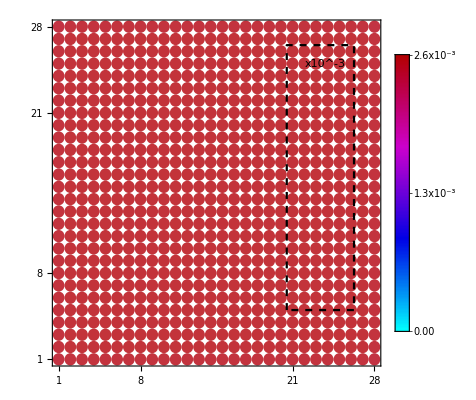

```mathematica
P2=Show[Graphics[{
PointSize[0.0001],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@FilteredData,

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,8,21,28},None}},BaseStyle-> 18,
PlotRange-> {{1,28},{1,28}},

Epilog-> {Inset[P1,{23.5,14}],Inset["x10^-3",{23.75,25}]}],
ListPlot[{{20.5,5},{20.5,26.5},{26.25,26.5},{26.25,5},{20.5,5}},Joined-> True,PlotStyle-> {Black,Dashed}]
]
```

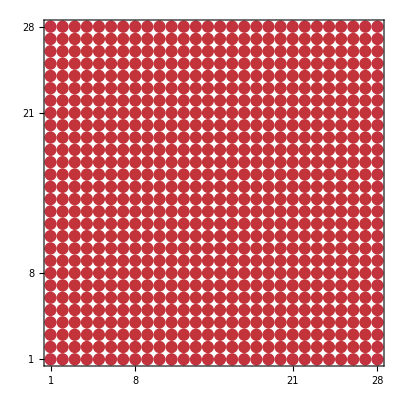

```mathematica
P2A=Show[Graphics[{
PointSize[0.04],colorfunc[#[[3]],rng[[2]]],Disk[#[[1;;2]],0.5]
}&/@FilteredData,


Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,8,21,28},None}},BaseStyle-> 18,
PlotRange-> {{1,28},{1,28}}
]]
```

```mathematica
Xaxis=Table[{{1,j},{28,j}},{j,1,28,1}];
```

```mathematica
Dimensions[Xaxis]
```

{28,2,2}

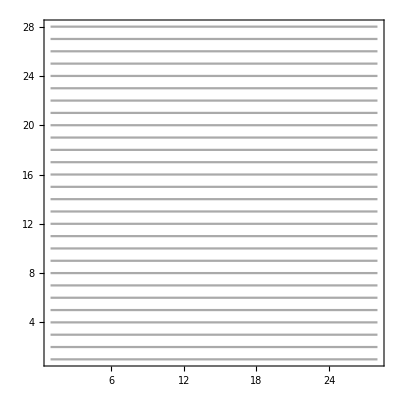

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,28}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,28},{1,28}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,8,21,28},None}},BaseStyle-> 18]
```

```mathematica
Yaxis1=Table[{{j,1},{j,28}},{j,1,28,1}];
```

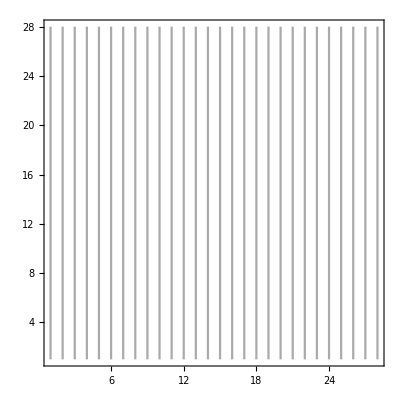

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,28}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,28},{1,28}},Frame-> True,Axes-> False,AspectRatio->1]
]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,8,21,28},None}},BaseStyle-> 18,
PlotRange-> {{1,28},{1,28}}
]]
```

-Graphics-

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

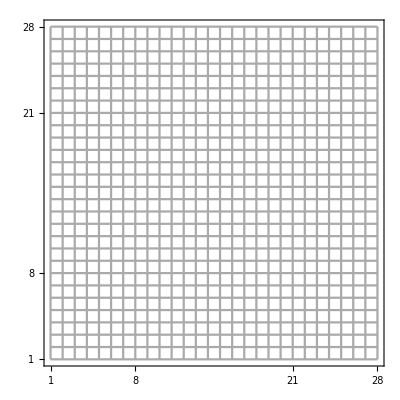

```mathematica
Show[P2B,P3,P4]
```

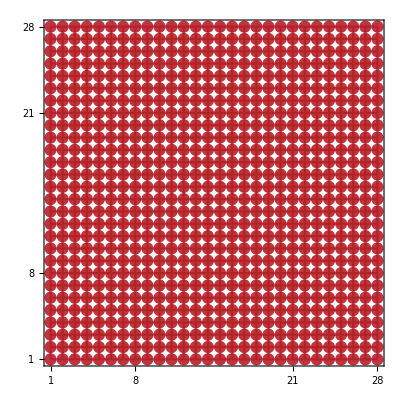

```mathematica
Show[P2B,P3,P4,P2A]
```